```mathematica
ps11b[n_,s_]:=(-n^(1/2-ⅈ s) (1/2+ⅈ s) HarmonicNumber[n,1/2-ⅈ s]+n^(1/2+ⅈ s) (1/2-ⅈ s) HarmonicNumber[n,1/2+ⅈ s])/(-n^(1/2-ⅈ s) (1/2+ⅈ s)+2^(1/2+ⅈ s) n^(1/2+ⅈ s) π^(-1/2+ⅈ s) (1/2-ⅈ s) Cos[1/2 π (1/2-ⅈ s)] Gamma[1/2-ⅈ s])
ps11c[n_,s_]:=ps11b[n,s I-I/2]
ps11d[n_,s_]:=(n^(1/2)(Sum[-n^(-ⅈ s) (1/2+ⅈ s) j^(-(1/2-ⅈ s))+n^(ⅈ s) (1/2-ⅈ s) j^(-(1/2+ⅈ s)),{j,1,n}]))/(-n^(1/2-ⅈ s) (1/2+ⅈ s)+2^(1/2+ⅈ s) n^(1/2+ⅈ s) π^(-1/2+ⅈ s) (1/2-ⅈ s) Cos[1/2 π (1/2-ⅈ s)] Gamma[1/2-ⅈ s])
ps11e[n_,s_]:=(n^(1/2)(Sum[j^(-1/2)(-n^(-ⅈ s) (1/2+ⅈ s) j^(ⅈ s)+n^(ⅈ s) (1/2-ⅈ s) j^(-ⅈ s)),{j,1,n}]))/(-n^(1/2-ⅈ s) (1/2+ⅈ s)+2^(1/2+ⅈ s) n^(1/2+ⅈ s) π^(-1/2+ⅈ s) (1/2-ⅈ s) Cos[1/2 π (1/2-ⅈ s)] Gamma[1/2-ⅈ s])
ps11f[n_,s_]:=(n^(1/2)(Sum[j^(-1/2)((1/2-ⅈ s) (n/j)^(ⅈ s)-(1/2+ⅈ s) (n/j)^(-ⅈ s)),{j,1,n}]))/(-n^(1/2-ⅈ s) (1/2+ⅈ s)+2^(1/2+ⅈ s) n^(1/2+ⅈ s) π^(-1/2+ⅈ s) (1/2-ⅈ s) Cos[1/2 π (1/2-ⅈ s)] Gamma[1/2-ⅈ s])
ps11g[n_,s_]:=(Sum[j^(-1/2)((1/2-ⅈ s) (n/j)^(ⅈ s)-(1/2+ⅈ s) (n/j)^(-ⅈ s)),{j,1,n}])/(-n^(-ⅈ s) (1/2+ⅈ s)+2^(1/2+ⅈ s) n^(+ⅈ s) π^(-1/2+ⅈ s) (1/2-ⅈ s) Cos[1/2 π (1/2-ⅈ s)] Gamma[1/2-ⅈ s])
ps11h[n_,s_]:=(Sum[j^(-1/2)((-I s)((n/j)^(ⅈ s)+(n/j)^(-ⅈ s))+(1/2)((n/j)^(ⅈ s)-(n/j)^(-ⅈ s))),{j,1,n}])/(-n^(-ⅈ s) (1/2+ⅈ s)+2^(1/2+ⅈ s) n^(+ⅈ s) π^(-1/2+ⅈ s) (1/2-ⅈ s) Cos[1/2 π (1/2-ⅈ s)] Gamma[1/2-ⅈ s])
ps11i[n_,s_]:=(I Sum[j^(-1/2)(2  s Cos[s Log[n/j]]- Sin[s Log[n/j]]),{j,1,n}])/(n^(-ⅈ s) (1/2+ⅈ s)-2^(1/2+ⅈ s) n^(+ⅈ s) π^(-1/2+ⅈ s) (1/2-ⅈ s) Cos[1/2 π (1/2-ⅈ s)] Gamma[1/2-ⅈ s])
ps11j[n_,s_]:=(I Sum[j^(-1/2)(2  s Cos[s Log[n/j]]- Sin[s Log[n/j]]),{j,1,n}])/((ⅈ s+1/2)n^(-ⅈ s) +(ⅈ s-1/2)n^(ⅈ s)2^(1/2+ⅈ s)  π^(-1/2+ⅈ s)  Cos[Pi/4-ⅈ s Pi/2] Gamma[1/2-ⅈ s])
ps11k[n_,s_]:=Sum[j^(-1/2)(2  s Cos[s Log[n/j]]- Sin[s Log[n/j]]),{j,1,n}]/((s-1/2 I)n^(-ⅈ s) +( s+1/2 I)n^(ⅈ s)2^(1/2+ⅈ s)  π^(-1/2+ⅈ s)  Cos[Pi/4-ⅈ s Pi/2] Gamma[1/2-ⅈ s])
ps11l[n_,s_]:=Sum[j^(-1/2)(2  s Cos[s Log[n/j]]- Sin[s Log[n/j]]),{j,1,n}]/(s(n^(-ⅈ s) +n^(ⅈ s)2^(1/2+ⅈ s)  π^(-1/2+ⅈ s)  Cos[Pi/4-ⅈ s Pi/2] Gamma[1/2-ⅈ s])+I/2(-n^(-ⅈ s) +n^(ⅈ s)2^(1/2+ⅈ s)  π^(-1/2+ⅈ s)  Cos[Pi/4-ⅈ s Pi/2] Gamma[1/2-ⅈ s]))
ps11m[n_,s_]:=Sum[j^(-1/2)(2  s Cos[s Log[n/j]]- Sin[s Log[n/j]]),{j,1,n}]/(s(n^(-ⅈ s) +n^(ⅈ s)2^(1/2+ⅈ s)  π^(-1/2+ⅈ s)  Cos[Pi/4-ⅈ s Pi/2] Gamma[1/2-ⅈ s])+I/2( n^(ⅈ s)2^(1/2+ⅈ s)  π^(-1/2+ⅈ s)  Cos[Pi/4-ⅈ s Pi/2] Gamma[1/2-ⅈ s]-n^(-ⅈ s)))
ps11n[n_,s_]:=Sum[j^(-1/2)(2  s Cos[s Log[n/j]]- Sin[s Log[n/j]]),{j,1,n}]/(s(E^(I s Log[n])2^(1/2+ⅈ s)  π^(-1/2+ⅈ s)  Cos[Pi/4-ⅈ s Pi/2] Gamma[1/2-ⅈ s]+E^(-I s Log[n]))+I/2( E^(I s Log[n])2^(1/2+ⅈ s)  π^(-1/2+ⅈ s)  Cos[Pi/4-ⅈ s Pi/2] Gamma[1/2-ⅈ s]-E^(-I s Log[n])))
ps11o[n_,s_]:=Sum[j^(-1/2)(2  s Cos[s Log[n/j]]- Sin[s Log[n/j]]),{j,1,n}]/(s(E^(I s Log[n])2^(1/2+ⅈ s)  π^(-1/2+ⅈ s)  Cos[Pi/4-ⅈ s Pi/2] Gamma[1/2-ⅈ s]+E^(-I s Log[n]))+I/2( E^(I s Log[n])2^(1/2+ⅈ s)  π^(-1/2+ⅈ s)  Cos[Pi/4-ⅈ s Pi/2] Gamma[1/2-ⅈ s]-E^(-I s Log[n])))



N@ps11o[10000,.3+4I]
```

1.053+0.0129554 ⅈ

```mathematica
N@ps11b[10000,.3+4I]
```

1.053+0.0129554 ⅈ

```mathematica
N@ps11jx[100000,.3+4I]
```

0.575524+0.107901 ⅈ

```mathematica
Zeta[.3+4I]
```

0.575756+0.10773 ⅈ

```mathematica
FullSimplify[1/2(E^(1/2 π (1/2-ⅈ s))+E^(-1/2 π (1/2-ⅈ s)))]
```

Cos[1/4 π (ⅈ+2 s)]

```mathematica
E^(I s Log[n]+(1/2+s I)Log[2]+(-1/2+s I)Log[Pi]) (1/2(E^(π/4-(ⅈ π s)/2)+E^(-π/4+(ⅈ π s)/2)))
```

(ⅇ^(-1/2 π (1/2-ⅈ s))+ⅇ^(1/2 π (1/2-ⅈ s))) n^(ⅈ s) (2 π)^(-1/2+ⅈ s)

```mathematica
E^(I s Log[n]+(1/2+s I)Log[2]+(-1/2+s I)Log[Pi])/2 (E^(π/4-(ⅈ π s)/2)+E^(-π/4+(ⅈ π s)/2))
```

```mathematica
(E^(I s Log[n]+(1/2+s I)Log[2]+(-1/2+s I)Log[Pi]+π/4-(ⅈ π s)/2)+E^(I s Log[n]+(1/2+s I)Log[2]+(-1/2+s I)Log[Pi]-π/4+(ⅈ π s)/2))/2
```

1/2 (ⅇ^(π/4-(ⅈ π s)/2+(1/2+ⅈ s) Log[2]+ⅈ s Log[n]+(-1/2+ⅈ s) Log[π])+ⅇ^(-π/4+(ⅈ π s)/2+(1/2+ⅈ s) Log[2]+ⅈ s Log[n]+(-1/2+ⅈ s) Log[π]))

```mathematica
FullSimplify[I s Log[n]+(1/2+s I)Log[2]+(-1/2+s I)Log[Pi]+π/4-(ⅈ π s)/2]
```

1/4 (π-2 ⅈ π s+Log[4/π^2]+4 ⅈ s Log[2 n π])

```mathematica
FullSimplify[I s Log[n]+(1/2+s I)Log[2]+(-1/2+s I)Log[Pi]-π/4+(ⅈ π s)/2]
```

1/4 (π (-1+2 ⅈ s)+Log[4/π^2]+4 ⅈ s Log[2 n π])

```mathematica
Cos[Pi/4-ⅈ s Pi/2]/.s->11
```

Cosh[(11/2+ⅈ/4) π]

```mathematica
N[-Sin[-ⅈ s Pi/2]/.s->11]
```

0.+1.59603×10^7 ⅈ

```mathematica
FullSimplify[2^(1/2+ⅈ s)  π^(-1/2+ⅈ s)  Cos[Pi/4-ⅈ s Pi/2] Gamma[1/2-ⅈ s]/.s->3I]
```

15/(64 π^3)

```mathematica
1/I
```

-ⅈ

```mathematica
fff[n_,s_]:=E^(I s Log[n])2^(1/2+ⅈ s)  π^(-1/2+ⅈ s)  Cos[Pi/4-ⅈ s Pi/2] Gamma[1/2-ⅈ s]+E^(-I s Log[n])
```

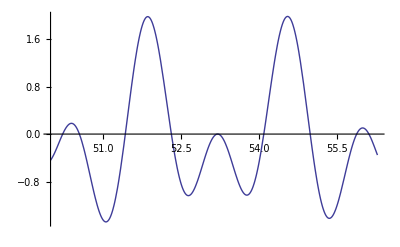

```mathematica
Plot[Re[fff[100,s] ],{s,50,50+2Pi}]
```

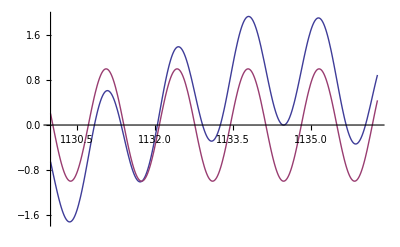

```mathematica
Plot[{Re[fff[100,s] ],Re[Cos[s Log[100] ]]},{s,1130,1130+2Pi}]
```